```mathematica
BarChart[{
Callout[Callout[100,"Below 30",Before],"Above 16"],
Callout[Callout[90,"30–50",Before],"13–16"],
Callout[Callout[80,"50–60",Before],"10–12"],
Callout[Callout[70,"60–70",Before],"8–9"],
Callout[Callout[60,"70–80",Before],"7"],
Callout[Callout[50,"80–90",Before],"6"],
Callout[Callout[30,"Above 90",Before],"Below 6"],
0
},
ChartLabels->Placed[{"Scientific","Academic","Quality","Digests","Slick fiction","Pulp fiction","Comics"},Center],
Axes->False,
ChartLayout->"Stacked",
LabelStyle->{FontFamily->"Optima"},
Epilog->{
Text[Style["Flesch\nReading Ease",{Bold,FontFamily->"Optima"}],{0,520}],
Text[Style["Grade\nLevel Formulas",{Bold,FontFamily->"Optima"}],{2.1,520}]
},
PlotRange->{{-0.3,4},{0,530}}
]
Export["~/Dropbox/Readability/draft/pdf/therm.pdf",%]
```

-Graphics-

~/Dropbox/Readability/draft/pdf/therm.pdf

```mathematica
Export["~/Dropbox/Readability/draft/pdf/therm.pdf",%]
```

-Graphics-

~/Dropbox/Readability/draft/pdf/therm.pdf

-Graphics-

```mathematica
?ImageCrop
```

RowBox[{"ImageCrop", "[", StyleBox["image", "TI"], "]"}] crops StyleBox["image", "TI"] by removing borders of uniform color. 
RowBox[{"ImageCrop", "[", RowBox[{StyleBox["image", "TI"], ",", StyleBox["size", "TI"]}], "]"}] crops StyleBox["image", "TI"] based on the size specification StyleBox["size", "TI"].
RowBox[{"ImageCrop", "[", RowBox[{StyleBox["image", "TI"], ",", StyleBox["size", "TI"], ",", StyleBox["spec", "TI"]}], "]"}] crops StyleBox["image", "TI"] by removing pixels from sides specified by StyleBox["spec", "TI"].

```mathematica
?ImageTrim
```

ImageTrim[image,{pt_1,pt_2,…}] gives the smallest subimage of image that includes all of the specified points.
ImageTrim[image,{pt_1,pt_2,…},r] adds a margin of size r back to the resulting image.

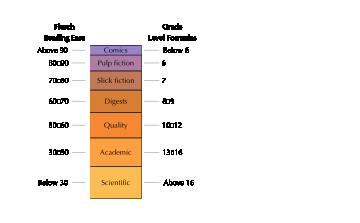

-Graphics-

~/Desktop/therm.pdf

```mathematica
Export["~/Desktop/therm.pdf",%]
Import["~/Desktop/therm.pdf"]
ImageCrop[%[[1]]]
Export["~/Desktop/therm.pdf",%]
```

```mathematica
?
```

```mathematica
?
```

```mathematica
?ImageCrop
```

ImageCrop[image] crops image by removing borders of uniform color. 
ImageCrop[image,size] crops image based on the size specification size.
ImageCrop[image,size,spec] crops image by removing pixels from sides specified by spec.

```mathematica
?Export
```

RowBox[{"Export", "[", RowBox[{StyleBox["\"\!\(\*StyleBox[\"file\",\"TI\"]\).\!\(\*StyleBox[\"ext\",\"TI\"]\)\"",ShowStringCharacters->True], ",", StyleBox["expr", "TI"]}], "]"}] exports data to a file, converting it to the format corresponding to the file extension StyleBox["ext", "TI"]. 
RowBox[{"Export", "[", RowBox[{StyleBox["file", "TI"], ",", StyleBox["expr", "TI"], ",", StyleBox["\"\!\(\*StyleBox[\"format\",\"TI\"]\)\"", ShowStringCharacters->True]}], "]"}] exports data in the specified format.
RowBox[{"Export", "[", RowBox[{StyleBox["file", "TI"], ",", StyleBox["exprs", "TI"], ",", StyleBox["elems", "TI"]}], "]"}] exports data by treating StyleBox["exprs", "TI"] as elements specified by StyleBox["elems", "TI"].
RowBox[{"Export", "[", RowBox[{StyleBox["file", "TI"], ",", StyleBox["expr", "TI"], ",", StyleBox["elems", "TI"], ",", StyleBox["relems", "TI"]}], "]"}] returns to StyleBox["the Wolfram System", "RebrandingTerm"] the elements specified by StyleBox["relems", "TI"].

~/Desktop/therm.pdf

```mathematica
?BarChart
```

BarChart[{y_1,y_2,…}] makes a bar chart with bar lengths y_1,  y_2, ….
BarChart[{…,w_i[y_i,…],…,w_j[y_j,…],…}] makes a bar chart with bar features defined by the symbolic wrappers w_k.
BarChart[{data_1,data_2,…}] makes a bar chart from multiple datasets data_i.

```mathematica
?Callout
```

Callout[data,expr] displays expr in a plot as a callout pointing to data.
Callout[data,expr,pos] displays a callout with expr at a position specified by pos.
Callout[data,expr,pos,apos] displays a callout anchored at a position specified by apos.

```mathematica
?BarChart
```

RowBox[{"BarChart", "[", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["y", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["y", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], "]"}] makes a bar chart with bar lengths SubscriptBox[StyleBox["y", "TI"], StyleBox["1", "TR"]], RowBox[{StyleBox[" ", "TI"], SubscriptBox[StyleBox["y", "TI"], StyleBox["2", "TR"]]}], ….
RowBox[{"BarChart", "[", RowBox[{"{", RowBox[{StyleBox["…", "TR"], ",", RowBox[{SubscriptBox[StyleBox["w", "TI"], StyleBox["i", "TI"]], "[", RowBox[{SubscriptBox[StyleBox["y", "TI"], StyleBox["i", "TI"]], ",", StyleBox["…", "TR"]}], "]"}], ",", StyleBox["…", "TR"], ",", RowBox[{SubscriptBox[StyleBox["w", "TI"], StyleBox["j", "TI"]], "[", RowBox[{SubscriptBox[StyleBox["y", "TI"], StyleBox["j", "TI"]], ",", StyleBox["…", "TR"]}], "]"}], ",", StyleBox["…", "TR"]}], "}"}], "]"}] makes a bar chart with bar features defined by the symbolic wrappers SubscriptBox[StyleBox["w", "TI"], StyleBox["k", "TI"]].
RowBox[{"BarChart", "[", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["data", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["data", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], "]"}] makes a bar chart from multiple datasets SubscriptBox[StyleBox["data", "TI"], StyleBox["i", "TI"]].

```mathematica
?Stacked
```

```mathematica
?Callout
```

Callout[data,expr] displays expr in a plot as a callout pointing to data.
Callout[data,expr,pos] displays a callout with expr at a position specified by pos.
Callout[data,expr,pos,apos] displays a callout anchored at a position specified by apos.